## Hubble Sphere, Particle Horizon, Event Horizon and Observable Universe

Equations used in this document are derived from Eq. (1.5.41) in Weinberg’s Cosmology book.

### Current Values

```mathematica
c=299792.458;(*km/s*)
H0=67.8;(*km/s/Mpc*)
Subscript[Ω, M]=0.3;Subscript[Ω, Λ]=0.7;Subscript[Ω, R]=0;Subscript[Ω, K]=0;
(*Hubble Sphere radius in Gly*)
Subscript[R, hs]=c/H0 3.2616*10^-3
(*Event Horizon radius in Gly*)
Subscript[R, Eh]=Subscript[R, hs] NIntegrate[1/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2),{a,1,1000000}]
(*Particle Horizon radius in Gly*)
Subscript[R, Ph]=Subscript[R, hs] NIntegrate[1/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2),{a,0,1}]
```

14.4219

16.4505

47.6654

### Age of the Universe

```mathematica
Subscript[T, 0]=NIntegrate[1/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a H0)(3.08567758*10^13*10^-3)/(3.15569*10^7),{a,0,1}](*Age of the universe in units "Billion years"*)
```

13.9043

### Evolution of comoving coordinates

Because the age of the universe t is a function of a, in order to plot the evolution of any physical quantity with time, we can also parametrize it with respect to a, so that we can plot it with respect to t.

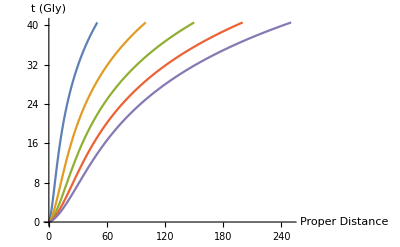

```mathematica
Subscript[t, a]=Table[NIntegrate[1/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a H0)(3.08567758*10^13*10^-3)/(3.15569*10^7),{a,0,aa}],{aa,0,5,0.01}];
a1=Thread[{Table[10a,{a,0,5,0.01}],Subscript[t, a]}];
a2=Thread[{Table[20a,{a,0,5,0.01}],Subscript[t, a]}];
a3=Thread[{Table[30a,{a,0,5,0.01}],Subscript[t, a]}];
a4=Thread[{Table[40a,{a,0,5,0.01}],Subscript[t, a]}];
a5=Thread[{Table[50a,{a,0,5,0.01}],Subscript[t, a]}];
ListLinePlot[{a1,a2,a3,a4,a5},AxesLabel->{"Proper Distance","t (Gly)"}]
```

### Hubble Sphere

#### Hubble constant is decreasing with time

```mathematica
Ht=Thread[{Table[(Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2),{a,10^-30,5,0.01}],Subscript[t, a]}];
ListLinePlot[Ht,AxesLabel->{"t (Gly)", "H"}]
```

-Graphics-

#### Hubble Sphere Radius

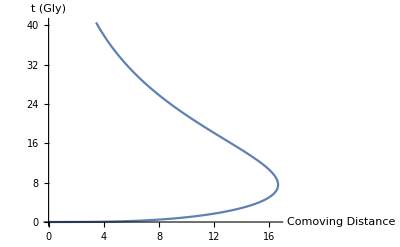

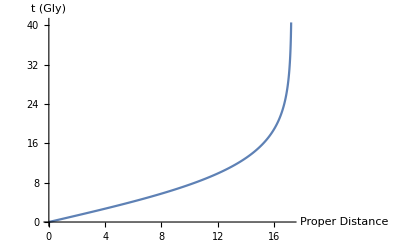

```mathematica
Hs=Table[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a),{a,10^-30,5,0.01}];(*Hubble sphere radius in proper distance D Subscript[(t), hs]=c/(H0(Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)), and the comoving distance is (D Subscript[(t), hs])/(a(t))*)
Hsco=Thread[{Hs,Subscript[t, a]}];
Hsprop=Thread[{Hs*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
ListLinePlot[Hsco,PlotRange->All,AxesLabel->{"Comoving Distance","t (Gly)"}]
ListLinePlot[Hsprop,AxesLabel->{"Proper Distance","t (Gly)"}]
```

### Particle Horizon

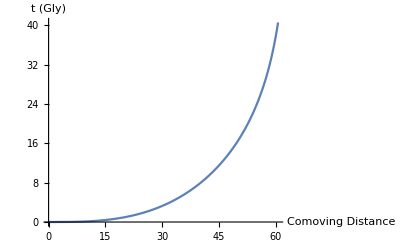

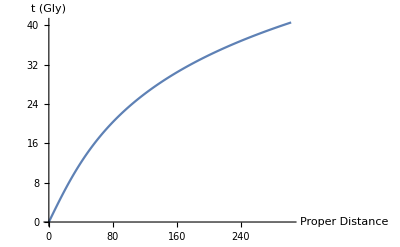

```mathematica
Ph=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,0,aa}],{aa,0,5,0.01}];
Phco=Thread[{Ph,Subscript[t, a]}];
Phprop=Thread[{Ph*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
ListLinePlot[Phco,AxesLabel->{"Comoving Distance","t (Gly)"}]
ListLinePlot[Phprop,AxesLabel->{"Proper Distance","t (Gly)"}]
```

### Event Horizon

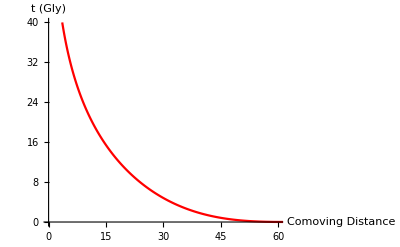

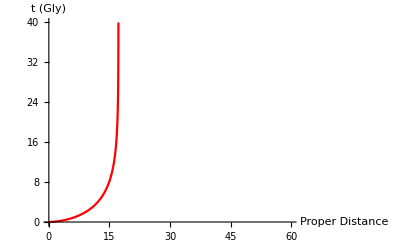

```mathematica
Eh=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,1000000}],{aa,0,5,0.01}];
Ehco=Thread[{Eh,Subscript[t, a]}];
Ehprop=Thread[{Eh*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
ListLinePlot[Ehco,PlotRange->{{0,60},{0,40}},PlotStyle->Red,AxesLabel->{"Comoving Distance","t (Gly)"}]
ListLinePlot[Ehprop,PlotRange->{{0,60},{0,40}},PlotStyle->Red,AxesLabel->{"Proper Distance","t (Gly)"}]
```

### Light cone

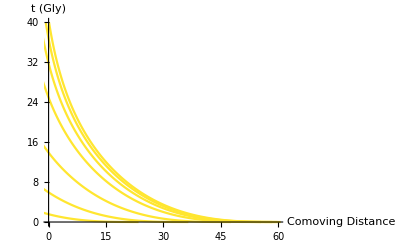

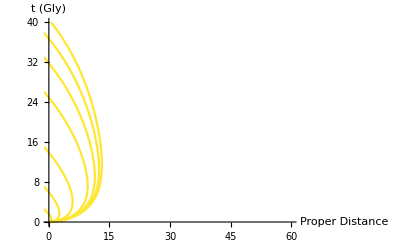

```mathematica
Lc02=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,0.2}],{aa,0,5,0.01}];
Lc05=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,0.5}],{aa,0,5,0.01}];
Lc=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,1}],{aa,0,5,0.01}];
Lc2=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,2}],{aa,0,5,0.01}];
Lc3=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,3}],{aa,0,5,0.01}];
Lc4=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,4}],{aa,0,5,0.01}];
Lc5=Table[NIntegrate[Subscript[R, hs]/((Subscript[Ω, Λ]+Subscript[Ω, K] a^-2+Subscript[Ω, M] a^-3+Subscript[Ω, R] a^-4)^(1/2)a^2)/.{Subscript[Ω, M]->0.3,Subscript[Ω, Λ]->0.7},{a,aa,5}],{aa,0,5,0.01}];
Lcco02=Thread[{Lc02,Subscript[t, a]}];
Lcco05=Thread[{Lc05,Subscript[t, a]}];
Lcco=Thread[{Lc,Subscript[t, a]}];
Lcco2=Thread[{Lc2,Subscript[t, a]}];
Lcco3=Thread[{Lc3,Subscript[t, a]}];
Lcco4=Thread[{Lc4,Subscript[t, a]}];
Lcco5=Thread[{Lc5,Subscript[t, a]}];
Lcprop02=Thread[{Lc02*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop05=Thread[{Lc05*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop=Thread[{Lc*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop2=Thread[{Lc2*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop3=Thread[{Lc3*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop4=Thread[{Lc4*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
Lcprop5=Thread[{Lc5*Table[a,{a,0,5,0.01}],Subscript[t, a]}];
ListLinePlot[{Lcco02,Lcco05,Lcco,Lcco2,Lcco3,Lcco4,Lcco5},PlotRange->{{0,60},{0,40}},PlotStyle->RGBColor[1.,0.9,0.19],AxesLabel->{"Comoving Distance","t (Gly)"}]
ListLinePlot[{Lcprop02,Lcprop05,Lcprop,Lcprop2,Lcprop3,Lcprop4,Lcprop5},PlotRange->{{0,60},{0,40}},PlotStyle->RGBColor[1.,0.9,0.19],AxesLabel->{"Proper Distance","t (Gly)"}]
```

### All in one plot

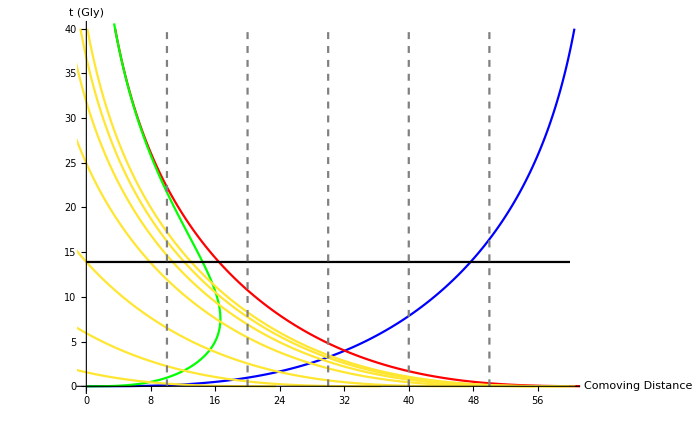

```mathematica
pco = Show[
ListLinePlot[Phco,PlotRange->{{0,60},{0,40}},PlotStyle->Blue,AxesLabel->{"Comoving Distance","t (Gly)"}],
ListLinePlot[Ehco,PlotRange->{{0,60},{0,40}},PlotStyle->Red],
ListLinePlot[Hsco,PlotRange->Automatic,PlotStyle->Green],
ListLinePlot[{Lcco02,Lcco05,Lcco,Lcco2,Lcco3,Lcco4,Lcco5},PlotRange->{{0,60},{0,40}},PlotStyle->RGBColor[1.,0.9,0.19]],
Plot[Subscript[T, 0],{t,0,60},PlotStyle->{Black,Bold}],
ParametricPlot[{{10,y},{20,y},{30,y},{40,y},{50,y}},{y,0,40},PlotStyle->{{Gray,Dashed}}]
]
```

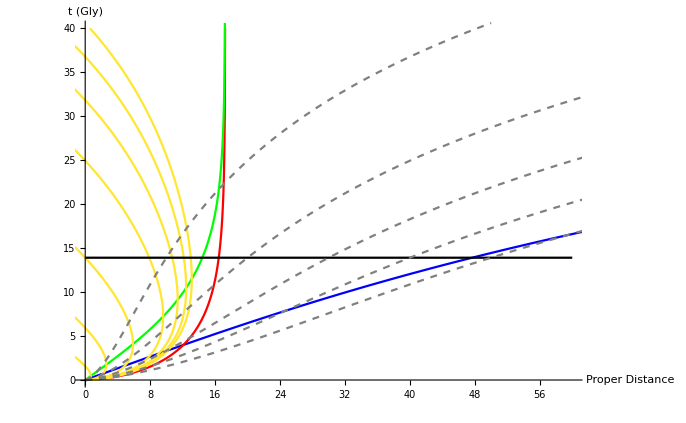

```mathematica
pprop = Show[
ListLinePlot[Phprop,PlotRange->{{0,60},{0,40}},PlotStyle->Blue,AxesLabel->{"Proper Distance","t (Gly)"}],
ListLinePlot[Ehprop,PlotRange->{{0,60},{0,40}},PlotStyle->Red],
ListLinePlot[Hsprop,PlotRange->Automatic,PlotStyle->Green],
ListLinePlot[{Lcprop02,Lcprop05,Lcprop,Lcprop2,Lcprop3,Lcprop4,Lcprop5},PlotRange->{{0,60},{0,40}},PlotStyle->RGBColor[1.,0.9,0.19]],
Plot[Subscript[T, 0],{t,0,60},PlotStyle->{Black,Bold}],
ListLinePlot[{a1,a2,a3,a4,a5},PlotStyle->{{Gray,Dashed}}]
]
```